given a table of n values

grazed shell with angle = 0

-Graphics-

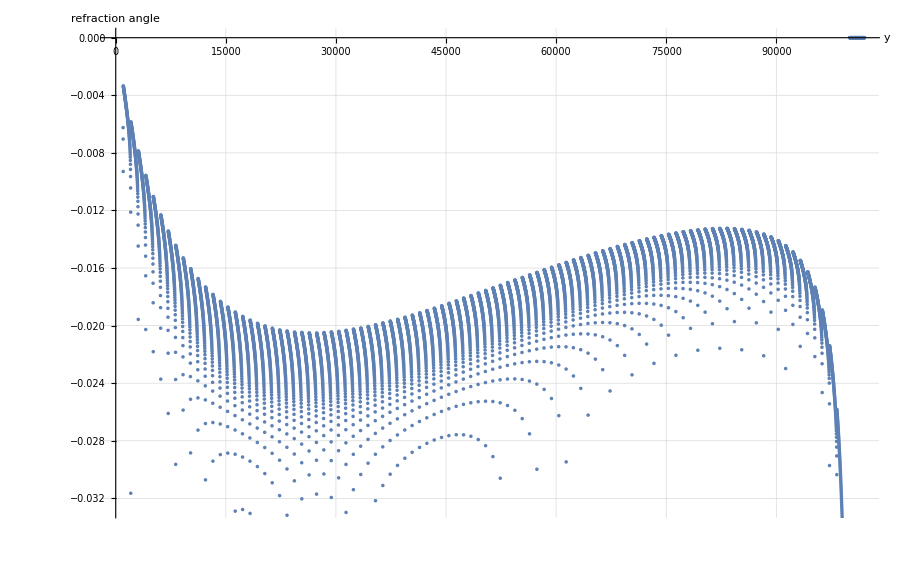

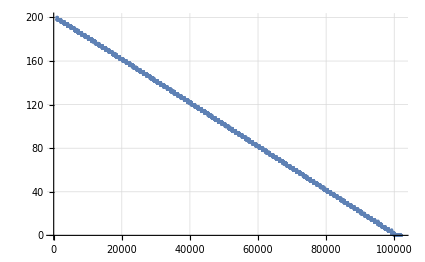

```mathematica
Clear["Global`*"];

(* Assumptions:
 shells are located around the origin
light rays never bend more than 90 degrees
*)

(* local gravity as a function of r *)
Gravity[r_]:=G*MPluto/r^2;

(* pressure as a function of height *)
Pressure[p0_,M_,h_,T_]:=p0 E^((-M Gravity[h+rSurf] h)/(k T));

(* Lorentz-Lorenz Equation for n values close to 1: returns a refractive index n given a temperature and pressure*)
LorentzLorenz[α_,p_,T_]:=√(1+(4π NAvagadro α p)/(R T)); 

(* shells are composed of the following: the circle graphic, the circle equation, the circle radius, the n value *)
(* more will be added to shells as we get into physical properties *)
Shell[r_,n_]:={Circle[{0,0},r],x^2+y^2==r^2,r,n}; 

(* calculate the normal angle of a shell based on location, assuming shells centered at 0,0) *)
NormalAngle[point_]:=ArcTan[point[[1]],point[[2]]]; 

(* refraction as a function of angles and rafractivity indicies *)
SnellsLaw[θin_,nin_,nout_]:=ArcSin[Sin[θin]nin/nout];

(* make an atmosphere with linearly-spaced shells specified by minimum, maximum, and step size of radius *)
MakeAtmosphere[min_,max_,step_,nTable_]:=Module[{r,center,nMax,nStep,n,i},
atmosphere={};

Which[
(* TODO - this which statement doesn't quite seem to work when both conditions are in... *)
(*
(* if nTable is null, use a linearly-varying n with nMax == 1.01 *)
((nTable==Null) || (NumberQ[nTable])),
{
Print["not given a table of n values"];
If[nTable==Null,
nMax = 1.01;
];
(* if nTable is an integer, use a linearly-varying n with nMax == nTable *)
If[NumberQ[nTable],
nMax = nTable;
];

nStep = (nMax-1.)/((max-min)/step);
n = nMax;
Do[
{
atmosphere =Append[atmosphere,Shell[r,n]];
n-=nStep;
},
{r,min,max,step}
];
},
*)
True,
(* we're actually given a table of n values *)
{
Print["given a table of n values"],
i = 1;
Do[
{
n=nTable[[i]];
atmosphere =Append[atmosphere,Shell[r,n]];
i+=1;
},
{r,min,max,step}
];
}
]
]

(* make the graphics objects *)
MakeAtmosphereGraphic[atm_]:=Table[Graphics[{Opacity[0.5],atmosphere[[i,1]]}],{i,1,Length[atm]}];

MakeIntersectionsPointsGraphic[intersections_]:=Graphics[{Red,Point[Table[{x/.intersections[[i]],y/.intersections[[i]]},{i,Length[intersections]}]]}];

FindNextShellIntersection[radius_,rayPosition_,rayAngle_]:=Module[{x0,y0,m,t1,t2,tList},
x0 = rayPosition[[1]];
y0 = rayPosition[[2]];
m=Tan[rayAngle];
t1 = (-x0-m y0 + √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);
t2 = (-x0-m y0 - √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);

(* return only real positive time values *)
tList=Select[{t1,t2},(#∈Reals&&#>TOL)&]
]

(* function that identifies where the light currently is in relation to shells *)
LocateLightRay[position_,atm_]:=Module[{shellRadii,posRadius},
{
shellRadii = atm[[All,3]];
posRadius = Norm[position];
Which[
(* entirely outside of shells *)
posRadius > Last[shellRadii],
rayLocation = "outside",

(* entirely inside the inner shell *)
posRadius < First[shellRadii],
rayLocation = "inside",

(* on outer shell *)
Abs[Last[shellRadii]- posRadius]<TOL,
rayLocation = "on outer shell",

True,
{
Do[
difference = Abs[posRadius-shellRadii[[i]]];
If[difference<TOL,
shellNum = i;
rayLocation="on";
Break[];,
rayLocation = "between";
];,
{i,Length[atm]}
]
}
]
};
rayLocation
]

(* updates the light position based on current position, direction, and shells *)
MoveLightRay[rayPath_,rayAngle_,atm_]:=Module[{location,tList,intersect,t,n2,position,posRadius},
position = Last[rayPath];
posRadius = Norm[position];

location  = LocateLightRay[position,atm];
Which[
(* only need to check the outermost shell *)
location == "outside",
{
t = Min[FindNextShellIntersection[Last[atm][[3]],position,rayAngle]];
},

(* only need to check the innermost shell *)
location == "inside",
{
t = Min[FindNextShellIntersection[First[atm][[3]],position,rayAngle]];
},

(* only need to check the second-outermost and itself shell unless it's a one-shell atmosphere *)
location == "on outer shell",
{
If[Length[atm]>1,
(* if it's a multi-shell atmosphere *)
{
t = Min[Join[
FindNextShellIntersection[atm[[-2,3]],position,rayAngle],
FindNextShellIntersection[atm[[-1,3]],position,rayAngle]
]
];
},

(* else if it's a single-shell atmosphere *)
{
t = Min[FindNextShellIntersection[atm[[1,3]],position,rayAngle]];
}
]
},

(* need to check the previous, current, and next shells *)
location == "on",
{
Do[
If[Abs[posRadius-atm[[All,3]][[i]]]<TOL,
shellNum = i;
Break[];,
];,
{i,Length[atm]}
];

If[shellNum==1,
(* if on inner shell *)
t = Min[Join[
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle]
]
],

(* if on some other shell *)
t = Min[Join[
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum-1,3]],position,rayAngle]
]
]
];
},

(* need to check the shells that it is between- now use currentShell as a counter *)
location == "between",
{
Print["warning: between atmosphere layers - this shouldn't really happen"];
shellNum =Length[atm];
While[atm[[shellNum,3]] > posRadius,
shellNum-=1; 
];
tList = Join[
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle]
];
t= Min[tList];
}
];

(* stuff to be done regardless of ray location case *)
(* non-intersection case *)
If[t==Infinity,
(*Print["t = infinity, location = " <> location];*)
t = 0.25, (* just set t to some small value (probably adjust to fit window size later *)
{}
];

intersect = {t+position[[1]],Tan[rayAngle ] t + position[[2]]};

position = intersect;

(* figure out which we're now interacting with *)
Do[
If[Abs[Norm[position]-atm[[All,3]][[i]]]<TOL,
(* get the refractivity of the shell *)
n2 = atm[[i,4]];
Break[];,

(* if we're not interacting with a shell, then we're back in vacuum with n2 = 1.0 *)
n2 = 1.0
];,
{i,Length[atm]}
];

AppendTo[intersectionPoints,position];
AppendTo[angleList,Refract[intersectionPoints,angleList,n2]]; 
position
]

(* refract based on entry and shell conditions using Snell's Law *)
Refract[rayPath_,angles_,n2_]:=Module[{newAngle,position,prevPosition,θ1,angle},
position = Last[rayPath];
prevPosition = rayPath[[-2]];

angle = Last[angles];
Which[
(* just grazed the top or bottom of a shell (no interaction), keep the angle the same *)
Abs[position[[1]]]<TOL,
{newAngle = angle;
Print["grazed shell with angle = " <> ToString[angle]];
},

(* hitting shell from outside in (radius decreasing) *)
Norm[position]<Norm[prevPosition],

(* TODO - I think this works now? *)
{
(*Print["outside in"];*)
θ1 = Mod[(π-NormalAngle[position]+angle),π/2];
newAngle = NormalAngle[position]-π+SnellsLaw[θ1,currentN,n2];
},
(* hitting shell from inside out *)
(* TODO - I think this condition works now? *)
(Norm[position]>Norm[prevPosition]) || (Norm[position]== Norm[prevPosition]),

{
(* Print["inside out"];*)
θ1=Mod[(NormalAngle[position]-angle),π/2];
newAngle = NormalAngle[position]-SnellsLaw[θ1,currentN,n2];
}
];
currentN=n2;
newAngle
]

(*run the program starting here *)
(*declare variables *)

TOL = 10^-9;
plutoRadius = 0.5;

(* physical constants *)
NAvagadro=6.022*10^23;  (* Avagadro's number *)
R=8.3145; (*J/mol K; universal gas constant*)
k = 1.3806488 ; (* m^2 kgs^-2 K^-1; Boltzmann constant *)
G = 6.67*10^-11; (* universal gravitational constant in mks units *)

αN2=1.71*10^-30;  (* m^3, mean polarizability of Subscript[N, 2] gas *)
μN2=0.028; (* kg; molar mass of Subscript[N, 2] *)

(* assumed properties of Pluto *)
p0 = 0.3; (* N/m^2; assumed surface pressure of Pluto *)
T = 50.; (* K; assumed atmospheric temperature for isothermal model *)
MPluto = 1.29*10^22; (* kg; mass of Pluto *)
rSurf = 11950000.; (* m; surface radius of Pluto *)

(* make the atmosphere *)
(*
atmMin = 1000.;
atmMax = 100000.;
atmStep = 1000.;
*)
atmMin = 1000.;
atmMax = 100000.;
atmStep = 1000.;

(* TODO putting in a dummy α value for now to produce results we can see *)
nTable = Table[LorentzLorenz[10^-23,Pressure[p0,μN2*10,h,T],T],{h,atmMin,atmMax,atmStep}];
MakeAtmosphere[atmMin,atmMax,atmStep,nTable];
(* TODO - using a linear thing for now *)

(* lists to store starting y coordinates and refraction angles *)
 startingY = {};
totalRefraction = {};
yVsRefraction = {};
dθOverdy={};
atmGraphics = {};
numIntersectionPoints = {};
Do[
temp = PrintTemporary["y multiplicative factor " <> ToString[yMultFact]]; (* for tracking progress *)

(* make a light ray *)
yStart = atmMax*yMultFact;
origin = {-atmMax*1.25,yStart}; (* origin needs to be specified by doubles rather than ints *)
angle = 0;
currentN = 1.0;

(* initialize lists of data *)
intersectionPoints = {origin};
angleList = {angle};

MoveLightRay[intersectionPoints,Last[angleList],atmosphere];

While[Norm[Last[intersectionPoints]]<= atmMax,
MoveLightRay[intersectionPoints,Last[angleList],atmosphere];
(*TODO need to extinguish light if it hits Pluto *)
(*TODO - actually, can't we just assume that the atmosphere starts at the ground and integrate from the ground up? *)
];

(* put the results in the appropriate lists *)
AppendTo[startingY,yStart];
AppendTo[totalRefraction,Last[angleList]];
AppendTo[yVsRefraction,{yStart,Last[angleList]}];

If[Length[startingY]>1,
AppendTo[dθOverdy,{yStart,(totalRefraction[[-2]]-totalRefraction[[-1]])/ (startingY[[-2]]-startingY[[-1]])}];
];

AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[intersectionPoints]}],ListLinePlot[intersectionPoints]}];
AppendTo[numIntersectionPoints,{yStart,Length[intersectionPoints]-2}]; (* minus 2 for start and end points*)

NotebookDelete[temp];,

(*{yMultFact,0.01,1.10,0.01}*)
{yMultFact,0.01,1.02,0.0001}
]


(* graphics stuff starts here *)
PlutoGraphic = Graphics[{GrayLevel[0.4],Disk[{0,0},0.5]}];
Show[MakeAtmosphereGraphic[atmosphere],atmGraphics] (* shell graphic *)
ListPlot[yVsRefraction,AxesLabel->{"y","refraction angle"},GridLines->Automatic]
ListPlot[intersectionPoints[[All,2]],AxesLabel-> {"x","y"}];
ListPlot[numIntersectionPoints,GridLines->Automatic]
ListPlot[dθOverdy];
```

```mathematica
atmosphere[[All,3]]
atmosphere[[All,4]]
```

{1000.,2000.,3000.,4000.,5000.,6000.,7000.,8000.,9000.,10000.,11000.,12000.,13000.,14000.,15000.,16000.,17000.,18000.,19000.,20000.,21000.,22000.,23000.,24000.,25000.,26000.,27000.,28000.,29000.,30000.,31000.,32000.,33000.,34000.,35000.,36000.,37000.,38000.,39000.,40000.,41000.,42000.,43000.,44000.,45000.,46000.,47000.,48000.,49000.,50000.,51000.,52000.,53000.,54000.,55000.,56000.,57000.,58000.,59000.,60000.,61000.,62000.,63000.,64000.,65000.,66000.,67000.,68000.,69000.,70000.,71000.,72000.,73000.,74000.,75000.,76000.,77000.,78000.,79000.,80000.,81000.,82000.,83000.,84000.,85000.,86000.,87000.,88000.,89000.,90000.,91000.,92000.,93000.,94000.,95000.,96000.,97000.,98000.,99000.,100000.}

{1.0263,1.02567,1.02506,1.02446,1.02388,1.02331,1.02276,1.02221,1.02169,1.02117,1.02066,1.02017,1.01969,1.01922,1.01877,1.01832,1.01788,1.01746,1.01704,1.01664,1.01624,1.01585,1.01548,1.01511,1.01475,1.0144,1.01406,1.01372,1.0134,1.01308,1.01277,1.01247,1.01217,1.01188,1.0116,1.01132,1.01105,1.01079,1.01054,1.01029,1.01004,1.00981,1.00957,1.00935,1.00912,1.00891,1.0087,1.00849,1.00829,1.00809,1.0079,1.00772,1.00753,1.00736,1.00718,1.00701,1.00685,1.00669,1.00653,1.00637,1.00622,1.00608,1.00593,1.00579,1.00566,1.00552,1.00539,1.00527,1.00514,1.00502,1.0049,1.00479,1.00468,1.00457,1.00446,1.00435,1.00425,1.00415,1.00405,1.00396,1.00387,1.00377,1.00369,1.0036,1.00352,1.00343,1.00335,1.00327,1.0032,1.00312,1.00305,1.00298,1.00291,1.00284,1.00277,1.00271,1.00265,1.00258,1.00252,1.00247}